# ICS Interaction Optimisation + Tuning Curves (Including Hourglass Effect)

SYMMETRIC i.e ROUND BEAMS ONLY! NEW COLLIMATED FLUX METHOD! VALID AT ANY CROSSING ANGLE!

## Setup + Base Equations

## Units, Constants, Cases + Optimisation Parameters

```mathematica
(*Units*)
```

```mathematica
MeV=10^6;
nm=10^-9;
mm=10^-3;
mrad=10^-3;
μrad=10^-6;
nrad=10^-9;
μm=10^-6;
pC=10^-12;
nC=10^-9;
μJ=10^-6;
MHz=10^6;
ps=10^-12;
```

```mathematica
(*Constants*)
```

```mathematica
me=0.51099895MeV;
h=4.135667696*10^-15; (*in eV*)
clight=299792458;
echarge=1.60217662*10^-19;
σT=6.6524587158*10^-29;
re=2.8179403262*10^-15;
fivedeg=(5*π)/180;
```

```mathematica
(*Cases*)
```

```mathematica
CBETA150 = {Ee->150MeV,λ->1064nm,ϵn->0.3mm mrad,ϕ->fivedeg,σL->25μm,Q->32pC,Epulse->62μJ,f->162.5MHz,tpulse->10ps,σze->1mm,ΔEe->5*10^-4,Δλ->6.57*10^-4};
headonCBETA150 = {Ee->150MeV,λ->1064nm,ϵn->0.3mm mrad,ϕ->0,σL->25μm,Q->32pC,Epulse->62μJ,f->162.5MHz,tpulse->10ps,σze->1mm,ΔEe->5*10^-4,Δλ->6.57*10^-4};

DIANA340={Ee->340MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
DIANA680={Ee->680MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
DIANA1020={Ee->1020MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};

headonDIANA687={Ee->687MeV,λ->1064nm,ϕ->0,Q->100pC,Epulse->100μJ,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};

MAXIIIeq={Ee->700MeV,λ->1064nm,ϕ->fivedeg,Q->0.996nC,Epulse->120μJ,ϵn->17.5471mm mrad,σL->25μm,tpulse->5.7ps,σze->0.0266815,f->83.33MHz,ΔEe->8.6*10^-4,Δλ->6.57*10^-4};
MAXIIIinj={Ee->700MeV,λ->1064nm,ϕ->fivedeg,Q->0.996nC,Epulse->120μJ,ϵn->1.398mm mrad,σL->25μm,tpulse->5.7ps,σze->0.0266815,f->83.33MHz,ΔEe->8.6*10^-4,Δλ->6.57*10^-4};
MAXIIIinjheadon={Ee->700MeV,λ->1064nm,ϕ->0,Q->0.996nC,Epulse->120μJ,ϵn->1.398mm mrad,σL->25μm,tpulse->5.7ps,σze->0.0266815,f->83.33MHz,ΔEe->8.6*10^-4,Δλ->6.57*10^-4};

HighMAXIIIinj={Ee->1520MeV,λ->1064nm,ϕ->fivedeg,Q->0.996nC,Epulse->120μJ,ϵn->1.398mm mrad,σL->25μm,tpulse->5.7ps,σze->0.0266815,f->83.33MHz,ΔEe->8.6*10^-4,Δλ->6.57*10^-4};

CLS300NdYAG={Ee->99.71MeV,λ->1064nm,ϕ->0,Q->100pC,Epulse->100μJ,ϵn->1mm mrad,σL->25μm,tpulse->5ps,σze->3mm,f->100MHz,ΔEe->8.6*10^-4,Δλ->6.5*10^-4};
CLS300HoYAG={Ee->99.71MeV,λ->2120nm,ϕ->0,Q->100pC,Epulse->100μJ,ϵn->1mm mrad,σL->25μm,tpulse->5ps,σze->3mm,f->100MHz,ΔEe->8.6*10^-4,Δλ->6.5*10^-4};
```

```mathematica
trialcase=CBETA150;
```

## Intermediaries

```mathematica
γ[Ee_]:=(Ee+me)/me;
β[Ee_]:=Sqrt[1-1/γ[Ee]^2];
EL[λ_]:=(h*clight)/λ;
ψ[Ee_,θ_]:=γ[Ee]*θ;
```

## Scattered Photon Energy

```mathematica
Eγ[Ee_,ϕ_,λ_,θ_]:=(EL[λ]*(1+β[Ee]*Cos[ϕ]))/(1-β[Ee]*Cos[θ]+EL[λ]/Ee*(1+Cos[ϕ+θ]));
```

```mathematica
Eγ[Ee,ϕ,λ,0]/.CBETA150
```

402517.

## Lorentz Invariants (from Mandelstam Variables)

```mathematica
X[Ee_,ϕ_,λ_]:=(2γ[Ee]*EL[λ]*(1+β[Ee]*Cos[ϕ]))/me;
Y[Ee_,ϕ_,λ_,θ_]:=(2*γ[Ee]*Eγ[Ee,ϕ,λ,θ]*(1-β[Ee]*Cos[θ]))/me;
```

## Cross Section, Luminosity + Collimated Flux

## Cross Section [Berestetskii, σ = f(Y)]

```mathematica
dσdY[Ee_,ϕ_,λ_,θ_]:=(8*π*re^2)/X[Ee,ϕ,λ]^2*((1/X[Ee,ϕ,λ]-1/Y[Ee,ϕ,λ,θ])^2+1/X[Ee,ϕ,λ]-1/Y[Ee,ϕ,λ,θ]+1/4*(X[Ee,ϕ,λ]/Y[Ee,ϕ,λ,θ]+Y[Ee,ϕ,λ,θ]/X[Ee,ϕ,λ]));
```

## Lorentz Invariant Y Differential [Me, Y = f(θ)]

```mathematica
dYdθ[Ee_,θ_,ϕ_,λ_]:=(X[Ee,ϕ,λ]*β[Ee]*Sin[θ]*(1-β[Ee]*Cos[θ]+(1+Cos[ϕ+θ])*EL[λ]/Ee)-X[Ee,ϕ,λ]*(1-β[Ee]*Cos[θ])*(β[Ee]*Sin[θ]-EL[λ]/Ee*Sin[ϕ+θ]))/(1-β[Ee]*Cos[θ]+(1+Cos[ϕ+θ])*EL[λ]/Ee)^2;
```

## Cross Section [Me, σ = f(θ)]

```mathematica
dσdθ[Ee_,ϕ_,λ_,θ_]:=dσdY[Ee,ϕ,λ,θ]*dYdθ[Ee,θ,ϕ,λ];
```

```mathematica
Off[NIntegrate::nlim,NIntegrate::inumr];
```

```mathematica
σ[Ee_,ϕ_,λ_,θcol_]:=NIntegrate[dσdθ[Ee,ϕ,λ,θ],{θ,0,θcol},Method->"Trapezoidal"];
```

```mathematica
σ[Ee,ϕ,λ,0.5mrad]/.trialcase//AbsoluteTiming
```

{0.0625993,2.08606×10^-30}

## Collimated Flux Intermediaries

```mathematica
(*Luminosity equations*)
Ne[Q_]:=Q/echarge;
NL[Epulse_,λ_]:=Epulse/(echarge*EL[λ]);
σe[βIP_,ϵn_,Ee_]:=Sqrt[(βIP*ϵn)/γ[Ee]];
σzl[tpulse_]:=clight*tpulse;
convxy[βIP_,ϵn_,Ee_,σL_]:=Sqrt[σe[βIP,ϵn,Ee]^2+σL^2];
convz[σze_,tpulse_]:=Sqrt[σze^2+σzl[tpulse]^2];
zr[σL_,λ_]:=(4*π*σL^2)/λ;
```

## Head-on Luminosity

```mathematica
L[Ee_,λ_,Q_,Epulse_,βIP_,ϵn_,σL_]:=(Ne[Q]*NL[Epulse,λ])/(2*π*convxy[βIP,ϵn,Ee,σL]^2);
```

## Angular Crossing + Hourglass Effect (Miyahara)

```mathematica
H[ϕ_,βIP_,Ee_,ϵn_,σL_,σze_,tpulse_]:=Cos[ϕ/2]*Sqrt[(convxy[βIP,ϵn,Ee,σL]^2*convxy[βIP,ϵn,Ee,σL]^2)/(π*convz[σze,tpulse]^2)];
Ux[βIP_,Ee_,ϵn_,σL_,λ_]:=Sqrt[1/2*(σe[βIP,ϵn,Ee]^2/βIP^2+σL^2/zr[σL,λ]^2)];
Uy[βIP_,Ee_,ϵn_,σL_,λ_]:=Sqrt[1/2*(σe[βIP,ϵn,Ee]^2/βIP^2+σL^2/zr[σL,λ]^2)];
hmiy[ϕ_,βIP_,Ee_,ϵn_,σL_,λ_,σze_,tpulse_,Zc_]:=Sin[ϕ/2]^2/(convxy[βIP,ϵn,Ee,σL]^2+Ux[βIP,Ee,ϵn,σL,λ]^2*Zc^2)+Cos[ϕ/2]^2/convz[σze,tpulse]^2;
```

```mathematica
RACHG[ϕ_,βIP_,Ee_,ϵn_,σL_,σze_,tpulse_,λ_]:=NIntegrate[(H[ϕ,βIP,Ee,ϵn,σL,σze,tpulse]*Exp[-hmiy[ϕ,βIP,Ee,ϵn,σL,λ,σze,tpulse,Zc]*Zc^2])/(Sqrt[convxy[βIP,ϵn,Ee,σL]^2+Ux[βIP,Ee,ϵn,σL,λ]^2*Zc^2]*Sqrt[convxy[βIP,ϵn,Ee,σL]^2+Uy[βIP,Ee,ϵn,σL,λ]^2*Zc^2]),{Zc,-0.1,0.1},Method->"Trapezoidal"];
```

```mathematica
RACHG[ϕ,0.1,Ee,ϵn,σL,σze,tpulse,λ]/.trialcase//AbsoluteTiming
```

{0.010147,0.191887}

## Collimated Flux

```mathematica
Fcol[Ee_,ϕ_,λ_,θcol_,βIP_,ϵn_,σL_,σze_,tpulse_,Q_,Epulse_,f_]:=σ[Ee,ϕ,λ,θcol]*RACHG[ϕ,βIP,Ee,ϵn,σL,σze,tpulse,λ]*L[Ee,λ,Q,Epulse,βIP,ϵn,σL]*f;
```

```mathematica
Fcol[Ee,ϕ,λ,0.5mrad,0.1,ϵn,σL,σze,tpulse,Q,Epulse,f]/.trialcase//AbsoluteTiming
```

{0.0189454,9.44706×10^8}

## Bandwidth

## Bandwidth Terms

```mathematica
collterm[Ee_,λ_,θ_,ϕ_]:=1/Sqrt[12]*ψ[Ee,θ]^2/(1+X[Ee,ϕ,λ]+ψ[Ee,θ]^2/2);
beamspreadterm[Ee_,λ_,ΔEe_,θ_,ϕ_]:=(2+X[Ee,ϕ,λ])/(1+X[Ee,ϕ,λ]+ψ[Ee,θ]^2)*ΔEe;
laserspreadterm[Ee_,λ_,Δλ_,θ_,ϕ_]:=(1+ψ[Ee,θ]^2)/(1+X[Ee,ϕ,λ]+ψ[Ee,θ]^2)*Δλ;
emittanceterm[Ee_,ϵn_,ϕ_,λ_,βIP_]:=(2*γ[Ee]*ϵn)/((1+X[Ee,ϕ,λ])*βIP);
```

## Bandwidth

```mathematica
bandwidth[Ee_,λ_,θ_,ϕ_,ΔEe_,Δλ_,ϵn_,βIP_]:=Sqrt[collterm[Ee,λ,θ,ϕ]^2+beamspreadterm[Ee,λ,ΔEe,θ,ϕ]^2+laserspreadterm[Ee,λ,Δλ,θ,ϕ]^2+emittanceterm[Ee,ϵn,ϕ,λ,βIP]^2];
```

## β^* Calculation

```mathematica
βstar[Ee_,ϵn_,BW_,λ_,ΔEe_,Δλ_,θ_,ϕ_]:=(2*γ[Ee]*ϵn)/((1+X[Ee,ϕ,λ])*Sqrt[BW^2-(collterm[Ee,λ,θ,ϕ]^2+beamspreadterm[Ee,λ,ΔEe,θ,ϕ]^2+laserspreadterm[Ee,λ,Δλ,θ,ϕ]^2)]);
```

# Single Fixed Bandwidth Optimisation

```mathematica
(*Optimisation Parameters*)
BW=0.5/100;
θmax=5mrad;
θstep=100nrad;(*100 nrad used for single cases (accurate enough! ~5 min)*)
```

## β^*-θ_col Pairings

```mathematica
βstardat=Table[{θ,Re[βstar[Ee,ϵn,BW,λ,ΔEe,Δλ,θ,ϕ]]/.trialcase},{θ,0,θmax,θstep}]//AbsoluteTiming;
simtime={βstardat⟦1⟧};
```

```mathematica
imaginarycut=Min[Position[βstardat⟦2⟧⟦All,2⟧,0.]]//AbsoluteTiming;
AppendTo[simtime,imaginarycut⟦1⟧];
```

```mathematica
βstardat=βstardat⟦2⟧⟦1;;(imaginarycut⟦2⟧-1),All⟧//AbsoluteTiming;
AppendTo[simtime,βstardat⟦1⟧];
```

β^*is calculated for each step in the range 0 to θmax. The position at which β^* becomes imaginary is found and then the imaginary values are discarded.

## Collimated Flux Maximisation

```mathematica
Off[NIntegrate::izero]
```

```mathematica
Fcoldat=Table[{βstardat⟦2⟧⟦i,1⟧,βstardat⟦2⟧⟦i,2⟧,Fcol[Ee,ϕ,λ,βstardat⟦2⟧⟦i,1⟧,βstardat⟦2⟧⟦i,2⟧,ϵn,σL,σze,tpulse,Q,Epulse,f]/.trialcase},{i,1,(imaginarycut⟦2⟧-1),1}]//AbsoluteTiming;
AppendTo[simtime,Fcoldat⟦1⟧];
```

```mathematica
maxval=Position[Fcoldat⟦2⟧⟦All,3⟧,Max[Fcoldat⟦2⟧⟦All,3⟧]]⟦1,1⟧;
```

## Results

```mathematica
Grid[{{"Parameter","Symbol","Value","Unit"},{"Target Bandwidth","ΔE_γ/E_γ",BW*100,"%"},{"Achieved Bandwidth","ΔE_γ/E_γ",bandwidth[Ee,λ,Fcoldat⟦2⟧⟦maxval,1⟧,ϕ,ΔEe,Δλ,ϵn,Fcoldat⟦2⟧⟦maxval,2⟧],"%"},{"Collimation Angle","θ_col",(Fcoldat⟦2⟧⟦maxval,1⟧)/mrad//N,"mrad"},{"β-function at the IP","β^*",Fcoldat⟦2⟧⟦maxval,2⟧,"m"},{"Collimated Flux","F_ψ",Fcoldat⟦2⟧⟦maxval,3⟧,"ph/s"},{"Simulation Time","t_sim",Total[simtime],"s"}},Dividers->{{True,True,True,True,True},{True,True,False,False,False,False,True}}]
```

Parameter | Symbol | Value | Unit
Bandwidth | ΔE_γ/E_γ | 0.5 | %
Collimation Angle | θ_col | 0.4333 | mrad
β-function at the IP | β^* | 0.125668 | m
Collimated Flux | F_ψ | 7.04026×10^8 | ph/s
Simulation Time | t_sim | 269.256 | s

# Tuning Curve Optimisation

```mathematica
(*Optimisation Parameters*)
BWmin=Sqrt[(2*ΔEe/.trialcase)^2+(Δλ/.trialcase)^2]; 
BWmax=1/100;
BWstep=10^-3/100;
θmax=2mrad;
θstep=0.32μrad;(*0.1μrad typically used for tuning curves, 0.32μrad takes 2hrs*)
```

## β^*-θ_col Pairings

Nested computations like nested tables can’t both be parallelized. Therefore, only the inner table (the more computationally intensive) is parallelized.

```mathematica
LaunchKernels[10];
```

```mathematica
DistributeDefinitions[βstar,BWmin,BWmax,BWstep,θmax,θstep];
```

```mathematica
βstardatcurve=Table[{BW,ParallelTable[{θ,Re[βstar[Ee,ϵn,BW,λ,ΔEe,Δλ,θ,ϕ]]/.trialcase},{θ,0,θmax,θstep}]},{BW,BWmin,BWmax,BWstep}]//AbsoluteTiming;
```

```mathematica
simtime={βstardatcurve⟦1⟧};
```

```mathematica
CloseKernels[];
```

```mathematica
imaginarycuts=Table[Min[Position[βstardatcurve⟦2⟧⟦i,2⟧⟦All,2⟧,0.]],{i,1,((BWmax-BWmin)/BWstep)}]//AbsoluteTiming;
AppendTo[simtime,imaginarycuts⟦1⟧];
```

```mathematica
βstardatcurve=Table[{βstardatcurve⟦2⟧⟦i,1⟧,βstardatcurve⟦2⟧⟦i,2⟧⟦1;;(imaginarycuts⟦2⟧⟦i⟧-1),All⟧},{i,1,((BWmax-BWmin)/BWstep)}]//AbsoluteTiming;
AppendTo[simtime,βstardatcurve⟦1⟧];
```

## Collimated Flux Maximisation

```mathematica
LaunchKernels[10];
```

```mathematica
DistributeDefinitions[Fcol,Fcoldatcurve,βstardatcurve,imaginarycuts,BWmax,BWmin,BWstep];
```

```mathematica
ParallelEvaluate[Off[NIntegrate::izero,NIntegrate::nlim,NIntegrate::inumr]];
```

```mathematica
Fcoldatcurve=Table[{βstardatcurve⟦2⟧⟦i,1⟧,ParallelTable[{βstardatcurve⟦2⟧⟦i,2⟧⟦j,1⟧,βstardatcurve⟦2⟧⟦i,2⟧⟦j,2⟧,Fcol[Ee,ϕ,λ,βstardatcurve⟦2⟧⟦i,2⟧⟦j,1⟧,βstardatcurve⟦2⟧⟦i,2⟧⟦j,2⟧,ϵn,σL,σze,tpulse,Q,Epulse,f]/.trialcase},{j,1,(imaginarycuts⟦2⟧⟦i⟧-1)}]},{i,1,((BWmax-BWmin)/BWstep)}]//AbsoluteTiming;
```

```mathematica
AppendTo[simtime,Fcoldatcurve⟦1⟧];
```

```mathematica
CloseKernels[];
```

```mathematica
maxvals=Table[Position[Fcoldatcurve⟦2⟧⟦i,2⟧⟦All,3⟧,Max[Fcoldatcurve⟦2⟧⟦i,2⟧⟦All,3⟧]]⟦1,1⟧,{i,1,((BWmax-BWmin)/BWstep)}]//AbsoluteTiming;
AppendTo[simtime,maxvals⟦1⟧];
```

```mathematica
maxdata=Table[{Fcoldatcurve⟦2⟧⟦i,1⟧*100,(Fcoldatcurve⟦2⟧⟦All,2⟧⟦i,maxvals⟦2⟧⟦i⟧,1⟧)/mrad,Fcoldatcurve⟦2⟧⟦All,2⟧⟦i,maxvals⟦2⟧⟦i⟧,2⟧,Fcoldatcurve⟦2⟧⟦All,2⟧⟦i,maxvals⟦2⟧⟦i⟧,3⟧},{i,1,((BWmax-BWmin)/BWstep)}]//AbsoluteTiming;
AppendTo[simtime,maxdata⟦1⟧];
```

The maxdata array is of the form BW, θcol, β^*, F_ψ . All of the necessary data is available in this singular array.

## Timing Data

```mathematica
Total[simtime]/60
```

76.1139

```mathematica
simtime
```

{456.961,2.39805,1.48466,4104.27,1.13011,0.591207}

## Tuning Curve Plots

```mathematica
FcolBWplot=ListLinePlot[Partition[Riffle[maxdata⟦2⟧⟦All,1⟧,maxdata⟦2⟧⟦All,4⟧],2],Frame->True,FrameLabel->{"Bandwidth (%)","Collimated Flux (ph/s)"},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},ImageSize->Medium];
```

```mathematica
βθplot=ListLinePlot[Partition[Riffle[maxdata⟦2⟧⟦All,2⟧,maxdata⟦2⟧⟦All,3⟧],2],Frame->True,FrameLabel->{"Collimation Angle (mrad))","β function at the IP (m)"},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotRange->All,ImageSize->Medium];
```

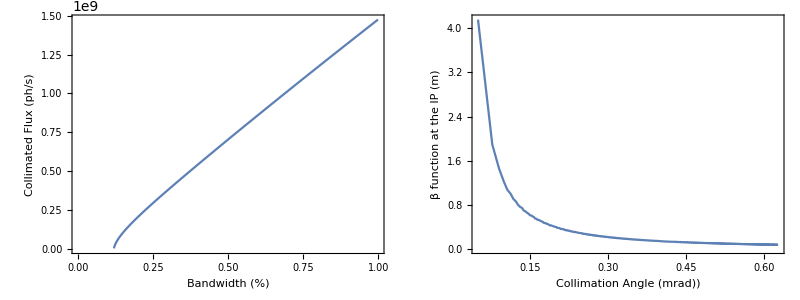

```mathematica
Grid[{{FcolBWplot,βθplot}}]
```